```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[g,GraphComplement[allGraphs5[29523,"graph"]]]
]&]
```

{19683,6561,2187,729,243,81,27,9,3,1}

```mathematica
allGraphs5[29523,"colofour"]
```

v1x2x3x45+v1x2x3x4x5

```mathematica
allGraphs5[1,"colofourrealnull"]
```

-n1x2x3x45+n1x2x3x4x5

```mathematica
Map[StringDrop[SymbolName[#],1]&,ListofVars[allGraphs5[1,"colofour"]]//Sort]//Length
```

37

```mathematica
{"1234x5","1235x4","123x4x5","124x35","124x3x5","125x34","125x3x4","12x34x5","12x35x4","12x3x4x5","134x25","134x2x5","135x24","135x2x4","13x24x5","13x25x4","13x2x4x5","14x235","14x23x5","14x25x3","14x2x35","14x2x3x5","15x234","15x23x4","15x24x3","15x2x34","15x2x3x4","1x234x5","1x235x4","1x23x4x5","1x24x35","1x24x3x5","1x25x34","1x25x3x4","1x2x34x5","1x2x35x4","1x2x3x4x5"}
```

```mathematica
Map[StringDrop[SymbolName[#],1]&,ListofVars[allGraphs5[29523,"colofourrealnull"]]//Sort]
```

{12345,1234x5,1235x4,123x4x5,1245x3,124x35,124x3x5,125x34,125x3x4,12x345,12x34x5,12x35x4,12x3x4x5,1345x2,134x25,134x2x5,135x24,135x2x4,13x245,13x24x5,13x25x4,13x2x4x5,145x23,145x2x3,14x235,14x23x5,14x25x3,14x2x35,14x2x3x5,15x234,15x23x4,15x24x3,15x2x34,15x2x3x4,1x2345,1x234x5,1x235x4,1x23x4x5,1x245x3,1x24x35,1x24x3x5,1x25x34,1x25x3x4,1x2x345,1x2x34x5,1x2x35x4,1x2x3x4x5}

```mathematica
Intersection[{"1234x5","1235x4","123x4x5","124x35","124x3x5","125x34","125x3x4","12x34x5","12x35x4","12x3x4x5","134x25","134x2x5","135x24","135x2x4","13x24x5","13x25x4","13x2x4x5","14x235","14x23x5","14x25x3","14x2x35","14x2x3x5","15x234","15x23x4","15x24x3","15x2x34","15x2x3x4","1x234x5","1x235x4","1x23x4x5","1x24x35","1x24x3x5","1x25x34","1x25x3x4","1x2x34x5","1x2x35x4","1x2x3x4x5"},{"12345","1234x5","1235x4","123x4x5","1245x3","124x35","124x3x5","125x34","125x3x4","12x345","12x34x5","12x35x4","12x3x4x5","1345x2","134x25","134x2x5","135x24","135x2x4","13x245","13x24x5","13x25x4","13x2x4x5","145x23","145x2x3","14x235","14x23x5","14x25x3","14x2x35","14x2x3x5","15x234","15x23x4","15x24x3","15x2x34","15x2x3x4","1x2345","1x234x5","1x235x4","1x23x4x5","1x245x3","1x24x35","1x24x3x5","1x25x34","1x25x3x4","1x2x345","1x2x34x5","1x2x35x4","1x2x3x4x5"}]//Length
```

37

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==8
]&]
```

{29520,29514,29512,29496,29494,29488,29442,29440,29434,29416,29280,29278,29272,29254,29200,28794,28792,28786,28768,28714,28552,27336,27334,27328,27310,27256,27094,26608,22962,22960,22954,22936,22882,22720,22234,20776,9840,9838,9832,9814,9760,9598,9112,7654,3280}

```mathematica
Take[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==8
]&],1]
```

{29520}

```mathematica
EdgeList[CompleteGraph[5]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeList[g]=={1<->4,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5}
]&]
```

{3037}

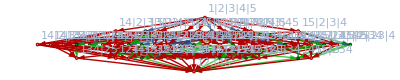

```mathematica
MobiusGraphDoubleGreen[K5Key,3037,allGraphs5]
```

```mathematica
EdgeList[EdgeDelete[CompleteGraph[5],{1<->2,1<->3,2<->3}]]
```

{1<->4,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5}

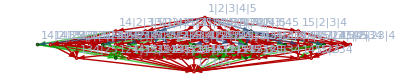
{{29520,-Graphics-,-Graphics-}→-Graphics-}

```mathematica
Table[{k,allGraphs5[k,"graph"],Graph[GraphComplement[allGraphs5[k,"graph"]],ImageSize->50,VertexLabels->"Name"]}->

MobiusGraphDoubleGreen[K5Key,k,allGraphs5],{k,Take[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==8
]&],1]}]
```

```mathematica
FindComplement[allGraphs_,key_]:=Block[{choices, compl=GraphComplement[allGraphs[key,"graph"]], edges, e,h,ands, result=-1},
choices=Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
IsomorphicGraphQ[g,compl]
]&&  allGraphs[key,"vertexsets"]==allGraphs[#,"vertexsets"]&
];
edges=EdgeList[allGraphs[key,"graph"]];
Table[
h=allGraphs[c,"graph"];
ands=Fold[And,Append[Table[!EdgeQ[h,e],{e,edges}],True]];
If[Evaluate[ands],
result=c
]
,
{c,choices}
];
result
]
```

```mathematica
FindComplement[allGraphs4,1]
```

363

```mathematica
allGraphs4[1,"graph"]
```

-Graphics-

```mathematica
allGraphs4[728,"graph"]
```

-Graphics-

```mathematica
comps=Monitor[Table[{k,FindComplement[allGraphs4,k]},{k,Keys[allGraphs4]}],k]//Sort
```

{{0,364},{1,363},{2,365},{3,361},{4,360},{6,367},{9,355},{10,354},{12,352},{13,351},{14,353},{16,357},{18,373},{22,369},{26,377},{27,337},{28,336},{30,334},{31,333},{36,328},{37,327},{39,325},{40,324},{45,346},{49,342},{54,391},{63,382},{72,400},{81,283},{82,282},{84,280},{85,279},{87,286},{90,274},{91,273},{93,271},{94,270},{97,276},{108,256},{109,255},{110,257},{111,253},{112,252},{117,247},{118,246},{120,244},{121,243},{122,245},{136,309},{145,300},{162,445},{165,442},{168,448},{190,417},{193,414},{218,473},{243,121},{244,120},{245,122},{246,118},{247,117},{252,112},{253,111},{255,109},{256,108},{257,110},{270,94},{271,93},{273,91},{274,90},{276,97},{279,85},{280,84},{282,82},{283,81},{286,87},{300,145},{309,136},{324,40},{325,39},{327,37},{328,36},{333,31},{334,30},{336,28},{337,27},{342,49},{346,45},{351,13},{352,12},{353,14},{354,10},{355,9},{357,16},{360,4},{361,3},{363,1},{364,0},{365,2},{367,6},{369,22},{373,18},{377,26},{382,63},{391,54},{400,72},{414,193},{417,190},{442,165},{445,162},{448,168},{473,218},{486,607},{487,606},{488,608},{516,577},{517,576},{546,637},{576,517},{577,516},{606,487},{607,486},{608,488},{637,546},{666,697},{697,666},{728,728}}

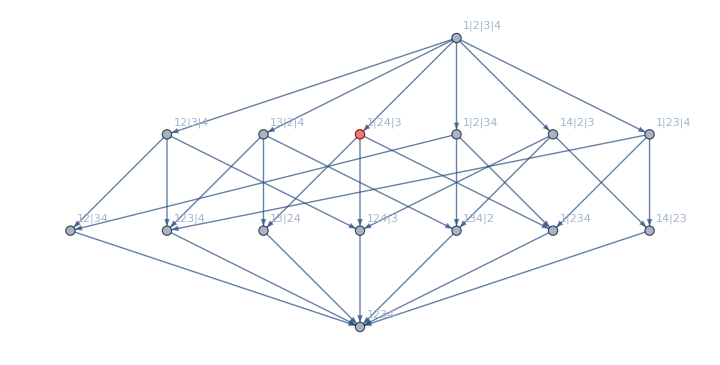

```mathematica
MobiusGraphDoubleGreen[K4Key,6,allGraphs4]
```

```mathematica
Select[comps,Greater[Length[allGraphs4[#[[1]],"colofour"]],Length[allGraphs4[#[[2]],"colofourrealnull"]]]&]
```

{}

```mathematica
Select[comps,Length[allGraphs4[#[[1]],"colofour"]]≠Length[allGraphs4[#[[2]],"colofourrealnull"]]&]
```

{{1,363},{3,361},{4,360},{9,355},{10,354},{12,352},{13,351},{14,353},{16,357},{22,369},{27,337},{28,336},{30,334},{36,328},{37,327},{39,325},{40,324},{45,346},{63,382},{81,283},{82,282},{84,280},{85,279},{87,286},{90,274},{93,271},{94,270},{108,256},{109,255},{110,257},{111,253},{112,252},{117,247},{118,246},{136,309},{165,442},{190,417},{243,121},{244,120},{245,122},{246,118},{247,117},{252,112},{253,111},{256,108},{270,94},{271,93},{273,91},{274,90},{276,97},{279,85},{282,82},{300,145},{324,40},{325,39},{327,37},{333,31},{334,30},{336,28},{342,49},{352,12},{354,10},{360,4},{414,193},{487,606},{516,577},{576,517}}

```mathematica
Select[comps,Length[allGraphs4[#[[1]],"colofour"]]==Length[allGraphs4[#[[2]],"colofourrealnull"]]&]
```

{{0,364},{2,365},{6,367},{18,373},{26,377},{31,333},{49,342},{54,391},{72,400},{91,273},{97,276},{120,244},{121,243},{122,245},{145,300},{162,445},{168,448},{193,414},{218,473},{255,109},{257,110},{280,84},{283,81},{286,87},{309,136},{328,36},{337,27},{346,45},{351,13},{353,14},{355,9},{357,16},{361,3},{363,1},{364,0},{365,2},{367,6},{369,22},{373,18},{377,26},{382,63},{391,54},{400,72},{417,190},{442,165},{445,162},{448,168},{473,218},{486,607},{488,608},{517,576},{546,637},{577,516},{606,487},{607,486},{608,488},{637,546},{666,697},{697,666},{728,728}}

```mathematica
TableForm[Table[{k,allGraphs4[k[[1]],"colofour"],allGraphs4[k[[2]],"colofourrealnull"]},{k,Take[Select[comps,Length[allGraphs4[#[[1]],"colofour"]]≠Length[allGraphs4[#[[2]],"colofourrealnull"]]&],2]}]]
```

1
363 | v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4 | -4 n1234+2 n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4
3
361 | v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4 | -4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4

```mathematica
TableForm[Table[{allGraphs4[k[[1]],"colofour"]//Length,allGraphs4[k[[2]],"colofourrealnull"]//Length},{k,comps}]]
```

15 | 15
10 | 13
5 | 5
10 | 13
7 | 10
5 | 5
10 | 13
7 | 10
7 | 10
4 | 8
3 | 4
3 | 4
5 | 5
3 | 4
2 | 2
10 | 13
7 | 10
7 | 10
5 | 5
7 | 12
5 | 8
5 | 8
3 | 4
3 | 4
2 | 2
5 | 5
3 | 4
2 | 2
10 | 13
7 | 10
7 | 12
5 | 8
3 | 4
7 | 10
5 | 5
5 | 8
3 | 4
2 | 2
7 | 10
4 | 8
3 | 4
5 | 8
3 | 4
5 | 8
3 | 4
4 | 4
2 | 2
2 | 2
3 | 4
2 | 2
5 | 5
3 | 4
2 | 2
3 | 4
2 | 2
2 | 2
10 | 13
7 | 12
3 | 4
7 | 10
5 | 8
7 | 10
5 | 8
5 | 5
3 | 4
2 | 2
7 | 10
5 | 8
4 | 8
3 | 4
3 | 4
5 | 8
4 | 4
3 | 4
2 | 2
2 | 2
3 | 4
2 | 2
7 | 10
5 | 8
5 | 8
4 | 4
4 | 8
3 | 4
3 | 4
2 | 2
3 | 4
2 | 2
5 | 5
3 | 4
2 | 2
3 | 4
2 | 2
2 | 2
3 | 4
2 | 2
2 | 2
0 | 0
0 | 0
0 | 0
2 | 2
0 | 0
0 | 0
2 | 2
0 | 0
0 | 0
3 | 4
2 | 2
2 | 2
0 | 0
0 | 0
0 | 0
5 | 5
3 | 4
2 | 2
3 | 4
2 | 2
2 | 2
3 | 4
2 | 2
2 | 2
0 | 0
0 | 0
0 | 0
2 | 2
0 | 0
0 | 0

```mathematica
Length[Select[comps,Length[allGraphs4[#[[1]],"colofour"]]==Length[allGraphs4[#[[2]],"colofourrealnull"]]&]]
```

60

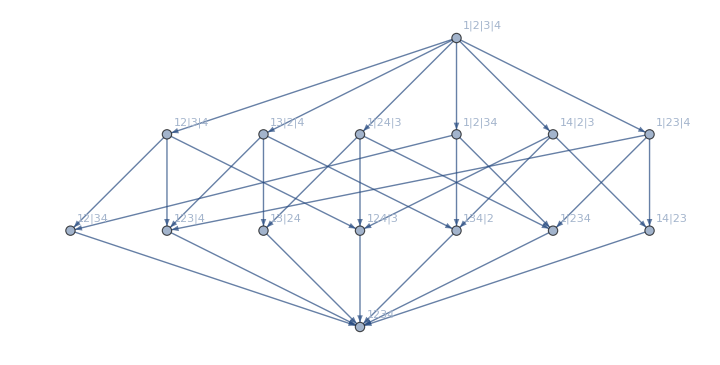
{-Graphics-{0,364},-Graphics-{2,365},-Graphics-{6,367},-Graphics-{18,373},-Graphics-{26,377},-Graphics-{31,333},-Graphics-{49,342},-Graphics-{54,391},-Graphics-{72,400},-Graphics-{91,273},-Graphics-{97,276},-Graphics-{120,244},-Graphics-{121,243},-Graphics-{122,245},-Graphics-{145,300},-Graphics-{162,445},-Graphics-{168,448},-Graphics-{193,414},-Graphics-{218,473},-Graphics-{255,109},-Graphics-{257,110},-Graphics-{280,84},-Graphics-{283,81},-Graphics-{286,87},-Graphics-{309,136},-Graphics-{328,36},-Graphics-{337,27},-Graphics-{346,45},-Graphics-{351,13},-Graphics-{353,14},-Graphics-{355,9},-Graphics-{357,16},-Graphics-{361,3},-Graphics-{363,1},-Graphics-{364,0},-Graphics-{365,2},-Graphics-{367,6},-Graphics-{369,22},-Graphics-{373,18},-Graphics-{377,26},-Graphics-{382,63},-Graphics-{391,54},-Graphics-{400,72},-Graphics-{417,190},-Graphics-{442,165},-Graphics-{445,162},-Graphics-{448,168},-Graphics-{473,218},-Graphics-{486,607},-Graphics-{488,608},-Graphics-{517,576},-Graphics-{546,637},-Graphics-{577,516},-Graphics-{606,487},-Graphics-{607,486},-Graphics-{608,488},-Graphics-{637,546},-Graphics-{666,697},-Graphics-{697,666},-Graphics-{728,728}}

```mathematica
Table[Labeled[MobiusGraphDoubleGreen[K4Key,k[[1]],allGraphs4],k],{k,Select[comps,Length[allGraphs4[#[[1]],"colofour"]]==Length[allGraphs4[#[[2]],"colofourrealnull"]]&]}]
```

```mathematica
ExpressionDifference[exp1_,exp2_]:=Block[{vars1, vars2},
vars1=Map[StringDrop[SymbolName[#],1]&, ListofVars[exp1]];
vars2=Map[StringDrop[SymbolName[#],1]&, ListofVars[exp2]];
Select[vars2,!MemberQ[vars1,#]&]
]
```

```mathematica
TableForm[Table[{ExpressionDifference[allGraphs4[k[[1]],"colofour"],allGraphs4[k[[2]],"colofourrealnull"]], allGraphs4[k[[1]],"colofour"], allGraphs4[k[[1]],"colofourrealnull"],allGraphs4[k[[2]],"colofourrealnull"]},{k,Select[comps,Length[allGraphs4[#[[1]],"colofour"]]!=Length[allGraphs4[#[[2]],"colofourrealnull"]]&]}]]
```

134x2
1x234
1234 | v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4 | -n1x2x34+n1x2x3x4 | -4 n1234+2 n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4
124x3
1x234
1234 | v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4 | -n1x24x3+n1x2x3x4 | -4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4
124x3
134x2
1234 | v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4 | n1x234-n1x24x3-n1x2x34+n1x2x3x4 | -2 n1234+2 n123x4+n124x3-n12x3x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4
123x4
1x234
1234 | v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4 | -n1x23x4+n1x2x3x4 | -4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4
123x4
134x2
1234 | v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4 | n1x234-n1x23x4-n1x2x34+n1x2x3x4 | -2 n1234+n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4
123x4
124x3
1234 | v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4 | n1x234-n1x23x4-n1x24x3+n1x2x3x4 | -2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4
123x4
124x3
134x2
1234 | v12x3x4+v13x2x4+v14x2x3+v1x2x3x4 | 2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n134x2-n13x2x4-n14x2x3+n1x2x3x4
1234 | v12x34+v134x2+v1x2x34 | -n1x234+n1x2x34 | n1234-n12x34-n134x2+n1x2x34
1234 | v124x3+v13x24+v1x24x3 | -n1x234+n1x24x3 | n1234-n124x3-n13x24+n1x24x3
1234 | v123x4+v14x23+v1x23x4 | -n1x234+n1x23x4 | n1234-n123x4-n14x23+n1x23x4
124x3
134x2
1234 | v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | -n14x2x3+n1x2x3x4 | -4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
124x3
1x234
1234 | v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4 | n134x2-n14x2x3-n1x2x34+n1x2x3x4 | -2 n1234+2 n123x4+n124x3-n12x3x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4
134x2
1x234
1234 | v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4 | n124x3-n14x2x3-n1x24x3+n1x2x3x4 | -2 n1234+2 n123x4+n12x34-n12x3x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4
123x4
124x3
134x2
1x234
1234 | v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4 | n14x23-n14x2x3-n1x23x4+n1x2x3x4 | -3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4
123x4
124x3
1234 | v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4 | -n1234+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n13x24-n13x2x4-n1x24x3+n1x2x3x4
123x4
134x2
1234 | v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4 | -n1234+n124x3+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4 | -n1234+n123x4+n12x34-n12x3x4+n134x2-n13x2x4-n1x2x34+n1x2x3x4
123x4 | v12x3x4+v13x2x4+v1x2x3x4 | -2 n1234+n124x3+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4 | n123x4-n12x3x4-n13x2x4+n1x2x3x4
1234 | v123x4+v1x234+v1x23x4 | -n14x23+n1x23x4 | n1234-n123x4-n1x234+n1x23x4
1234 | v124x3+v134x2+v14x2x3 | -n14x23+n14x2x3 | n1234-n124x3-n134x2+n14x2x3
123x4
134x2
1234 | v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | -n13x2x4+n1x2x3x4 | -4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
123x4
1x234
1234 | v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4 | n134x2-n13x2x4-n1x2x34+n1x2x3x4 | -2 n1234+n123x4+2 n124x3-n12x3x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4
123x4
124x3
134x2
1x234
1234 | v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4 | n13x24-n13x2x4-n1x24x3+n1x2x3x4 | -3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4
123x4
124x3
1234 | v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4 | -n1234+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4
1234 | v124x3+v1x234+v1x24x3 | -n13x24+n1x24x3 | n1234-n124x3-n1x234+n1x24x3
134x2
1x234
1234 | v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4 | n123x4-n13x2x4-n1x23x4+n1x2x3x4 | -2 n1234+2 n124x3+n12x34-n12x3x4+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4
124x3
134x2
1234 | v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4 | -n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4 | -n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4
124x3 | v12x3x4+v14x2x3+v1x2x3x4 | -2 n1234+n123x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4 | n124x3-n12x3x4-n14x2x3+n1x2x3x4
123x4
124x3
1234 | v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | n134x2-n13x2x4-n14x2x3+n1x2x3x4 | -2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
123x4
124x3
1x234
1234 | v12x3x4+v1x23x4+v1x24x3+v1x2x3x4 | 2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4
1234 | v12x34+v1x234+v1x2x34 | -n134x2+n1x2x34 | n1234-n12x34-n1x234+n1x2x34
123x4
1x234
1234 | v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4 | -n1234+n124x3+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4 | -n1234+n123x4+n12x34-n12x3x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4
123x4 | v12x3x4+v1x23x4+v1x2x3x4 | -2 n1234+n124x3+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4 | n123x4-n12x3x4-n1x23x4+n1x2x3x4
124x3
1x234
1234 | v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4 | -n1234+n123x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4 | -n1234+n124x3+n12x34-n12x3x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4
124x3 | v12x3x4+v1x24x3+v1x2x3x4 | -2 n1234+n123x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4 | n124x3-n12x3x4-n1x24x3+n1x2x3x4
1234 | v124x3+v14x23+v14x2x3 | -n134x2+n14x2x3 | n1234-n124x3-n14x23+n14x2x3
1234 | v123x4+v134x2+v13x2x4 | -n13x24+n13x2x4 | n1234-n123x4-n134x2+n13x2x4
1234 | v123x4+v13x24+v13x2x4 | -n134x2+n13x2x4 | n1234-n123x4-n13x24+n13x2x4
123x4
124x3
1234 | v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | -n12x3x4+n1x2x3x4 | -4 n1234+n123x4+n124x3+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
123x4
124x3
134x2
1x234
1234 | v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4 | n12x34-n12x3x4-n1x2x34+n1x2x3x4 | -3 n1234+n123x4+n124x3+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4
1234 | v134x2+v1x234+v1x2x34 | -n12x34+n1x2x34 | n1234-n134x2-n1x234+n1x2x34
123x4
1x234
1234 | v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4 | n124x3-n12x3x4-n1x24x3+n1x2x3x4 | -2 n1234+n123x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4
123x4
134x2
1234 | v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4 | -n1234+n124x3+n12x34-n12x3x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4 | -n1234+n123x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4
124x3
1x234
1234 | v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4 | n123x4-n12x3x4-n1x23x4+n1x2x3x4 | -2 n1234+n124x3+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4
124x3
134x2
1234 | v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4 | -n1234+n123x4+n12x34-n12x3x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4 | -n1234+n124x3+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4
134x2 | v13x2x4+v14x2x3+v1x2x3x4 | -2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4 | n134x2-n13x2x4-n14x2x3+n1x2x3x4
123x4
134x2
1234 | v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | n124x3-n12x3x4-n14x2x3+n1x2x3x4 | -2 n1234+n123x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
123x4
1x234
1234 | v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4 | -n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4 | -n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4
123x4
134x2
1x234
1234 | v13x2x4+v1x23x4+v1x2x34+v1x2x3x4 | 2 n124x3-n12x3x4-n14x2x3-n1x24x3+n1x2x3x4 | -n1234+n123x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4
123x4 | v13x2x4+v1x23x4+v1x2x3x4 | -2 n1234+2 n124x3+n12x34-n12x3x4+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4 | n123x4-n13x2x4-n1x23x4+n1x2x3x4
1234 | v13x24+v1x234+v1x24x3 | -n124x3+n1x24x3 | n1234-n13x24-n1x234+n1x24x3
134x2
1x234
1234 | v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4 | -n1234+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4
134x2 | v13x2x4+v1x2x34+v1x2x3x4 | -2 n1234+n123x4+2 n124x3-n12x3x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4 | n134x2-n13x2x4-n1x2x34+n1x2x3x4
1234 | v134x2+v14x23+v14x2x3 | -n124x3+n14x2x3 | n1234-n134x2-n14x23+n14x2x3
124x3
134x2
1234 | v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4 | n123x4-n12x3x4-n13x2x4+n1x2x3x4 | -2 n1234+n124x3+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4
124x3
1x234
1234 | v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4 | -n1234+n123x4+n12x34-n12x3x4+n134x2-n13x2x4-n1x2x34+n1x2x3x4 | -n1234+n124x3+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4
134x2
1x234
1234 | v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4 | -n1234+n123x4+n124x3-n12x3x4+n13x24-n13x2x4-n1x24x3+n1x2x3x4 | -n1234+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4
124x3
134x2
1x234
1234 | v14x2x3+v1x24x3+v1x2x34+v1x2x3x4 | 2 n123x4-n12x3x4-n13x2x4-n1x23x4+n1x2x3x4 | -n1234+n124x3+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4
124x3 | v14x2x3+v1x24x3+v1x2x3x4 | -2 n1234+2 n123x4+n12x34-n12x3x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4 | n124x3-n14x2x3-n1x24x3+n1x2x3x4
134x2 | v14x2x3+v1x2x34+v1x2x3x4 | -2 n1234+2 n123x4+n124x3-n12x3x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4 | n134x2-n14x2x3-n1x2x34+n1x2x3x4
1234 | v14x23+v1x234+v1x23x4 | -n123x4+n1x23x4 | n1234-n14x23-n1x234+n1x23x4
1x234 | v1x23x4+v1x24x3+v1x2x3x4 | -2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4 | n1x234-n1x23x4-n1x24x3+n1x2x3x4
1x234 | v1x23x4+v1x2x34+v1x2x3x4 | -2 n1234+n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4 | n1x234-n1x23x4-n1x2x34+n1x2x3x4
1x234 | v1x24x3+v1x2x34+v1x2x3x4 | -2 n1234+2 n123x4+n124x3-n12x3x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4 | n1x234-n1x24x3-n1x2x34+n1x2x3x4
1234 | v134x2+v13x24+v13x2x4 | -n123x4+n13x2x4 | n1234-n134x2-n13x24+n13x2x4
1234 | v123x4+v124x3+v12x3x4 | -n12x34+n12x3x4 | n1234-n123x4-n124x3+n12x3x4
1234 | v123x4+v12x34+v12x3x4 | -n124x3+n12x3x4 | n1234-n123x4-n12x34+n12x3x4
1234 | v124x3+v12x34+v12x3x4 | -n123x4+n12x3x4 | n1234-n124x3-n12x34+n12x3x4

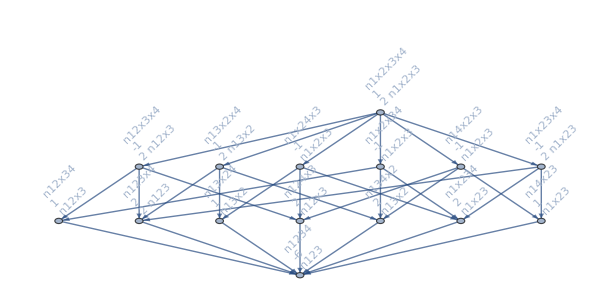

```mathematica
MobiusGraph4[K4Key,allGraphs4]
```

```mathematica
Select[Keys[allGraphs4],Greater[Length[Intersection[ListofVars[allGraphs4[#,"colofour"]],ListofVars[(v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4)+(v1x2x34+v1x2x3x4)]]],10]&]
```

{0}

```mathematica
ListofVars[(v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4)+(v1x2x34+v1x2x3x4)]//Length
```

11

```mathematica
comps5=Monitor[Table[{k,FindComplement[allGraphs5,k]},{k,Keys[allGraphs5]}],k]//Sort
```

{{0,29524},{1,29523},{2,29525},{3,29521},{4,29520},{6,29527},{9,29515},{10,29514},{12,29512},{13,29511},{14,29513},{16,29517},{18,29533},{22,29529},{26,29537},{27,29497},{28,29496},{30,29494},{31,29493},{36,29488},{37,29487},{39,29485},{40,29484},{45,29506},{49,29502},{54,29551},{63,29542},{72,29560},{81,29443},{82,29442},{84,29440},{85,29439},{87,29446},{90,29434},{91,29433},{93,29431},{94,29430},{97,29436},{108,29416},{109,29415},{110,29417},{111,29413},{112,29412},{117,29407},{118,29406},{120,29404},{121,29403},{122,29405},{136,29469},{145,29460},{162,29605},{165,29602},{168,29608},{190,29577},{193,29574},{218,29633},{243,29281},{244,29280},{245,29282},{246,29278},{247,29277},{252,29272},{253,29271},{255,29269},{256,29268},{257,29270},{270,29254},{271,29253},{273,29251},{274,29250},{276,29257},{279,29245},{280,29244},{282,29242},{283,29241},{286,29247},{300,29305},{309,29296},{324,29200},{325,29199},{327,29197},{328,29196},{333,29191},{334,29190},{336,29188},{337,29187},{342,29209},{346,29205},{351,29173},{352,29172},{353,29174},{354,29170},{355,29169},{357,29176},{360,29164},{361,29163},{363,29161},{364,29160},{365,29162},{367,29166},{369,29182},{373,29178},{377,29186},{382,29223},{391,29214},{400,29232},{414,29353},{417,29350},{442,29325},{445,29322},{448,29328},{473,29378},{486,29767},{487,29766},{488,29768},{516,29737},{517,29736},{546,29797},{576,29677},{577,29676},{606,29647},{607,29646},{608,29648},{637,29706},{666,29857},{697,29826},{728,29888},{729,28795},{730,28794},{732,28792},{733,28791},{738,28786},{739,28785},{741,28783},{742,28782},{747,28804},{751,28800},{756,28768},{757,28767},{759,28765},{760,28764},{765,28759},{766,28758},{768,28756},{769,28755},{774,28777},{778,28773},{810,28714},{811,28713},{813,28711},{814,28710},{819,28705},{820,28704},{822,28702},{823,28701},{837,28687},{838,28686},{840,28684},{841,28683},{846,28678},{847,28677},{849,28675},{850,28674},{891,28876},{894,28873},{919,28848},{922,28845},{972,28552},{973,28551},{975,28549},{976,28548},{981,28543},{982,28542},{984,28540},{985,28539},{999,28525},{1000,28524},{1002,28522},{1003,28521},{1008,28516},{1009,28515},{1011,28513},{1012,28512},{1053,28471},{1054,28470},{1056,28468},{1057,28467},{1062,28462},{1063,28461},{1065,28459},{1066,28458},{1071,28480},{1075,28476},{1080,28444},{1081,28443},{1083,28441},{1084,28440},{1089,28435},{1090,28434},{1092,28432},{1093,28431},{1098,28453},{1102,28449},{1143,28624},{1146,28621},{1171,28596},{1174,28593},{1215,29038},{1216,29037},{1245,29008},{1246,29007},{1305,28948},{1306,28947},{1335,28918},{1336,28917},{1395,29128},{1426,29097},{1458,30253},{1467,30244},{1476,30262},{1539,30172},{1548,30163},{1620,30334},{1701,30010},{1710,30001},{1782,29929},{1791,29920},{1800,29938},{1872,30082},{1944,30496},{2034,30406},{2124,30586},{2187,27337},{2188,27336},{2190,27334},{2191,27333},{2193,27340},{2196,27328},{2197,27327},{2199,27325},{2200,27324},{2203,27330},{2214,27310},{2215,27309},{2217,27307},{2218,27306},{2223,27301},{2224,27300},{2226,27298},{2227,27297},{2241,27364},{2250,27355},{2268,27256},{2269,27255},{2271,27253},{2272,27252},{2274,27259},{2277,27247},{2278,27246},{2280,27244},{2281,27243},{2284,27249},{2295,27229},{2296,27228},{2298,27226},{2299,27225},{2304,27220},{2305,27219},{2307,27217},{2308,27216},{2323,27282},{2332,27273},{2430,27094},{2431,27093},{2433,27091},{2434,27090},{2439,27085},{2440,27084},{2442,27082},{2443,27081},{2457,27067},{2458,27066},{2460,27064},{2461,27063},{2463,27070},{2466,27058},{2467,27057},{2469,27055},{2470,27054},{2473,27060},{2487,27118},{2496,27109},{2511,27013},{2512,27012},{2514,27010},{2515,27009},{2520,27004},{2521,27003},{2523,27001},{2524,27000},{2538,26986},{2539,26985},{2541,26983},{2542,26982},{2544,26989},{2547,26977},{2548,26976},{2550,26974},{2551,26973},{2554,26979},{2569,27036},{2578,27027},{2673,27580},{2674,27579},{2703,27550},{2704,27549},{2733,27610},{2763,27490},{2764,27489},{2793,27460},{2794,27459},{2824,27519},{2916,26608},{2917,26607},{2918,26609},{2919,26605},{2920,26604},{2925,26599},{2926,26598},{2928,26596},{2929,26595},{2930,26597},{2943,26581},{2944,26580},{2946,26578},{2947,26577},{2952,26572},{2953,26571},{2955,26569},{2956,26568},{2997,26527},{2998,26526},{3000,26524},{3001,26523},{3006,26518},{3007,26517},{3009,26515},{3010,26514},{3024,26500},{3025,26499},{3026,26501},{3027,26497},{3028,26496},{3033,26491},{3034,26490},{3036,26488},{3037,26487},{3038,26489},{3159,26365},{3160,26364},{3161,26366},{3162,26362},{3163,26361},{3168,26356},{3169,26355},{3171,26353},{3172,26352},{3173,26354},{3186,26338},{3187,26337},{3189,26335},{3190,26334},{3195,26329},{3196,26328},{3198,26326},{3199,26325},{3240,26284},{3241,26283},{3243,26281},{3244,26280},{3249,26275},{3250,26274},{3252,26272},{3253,26271},{3267,26257},{3268,26256},{3269,26258},{3270,26254},{3271,26253},{3276,26248},{3277,26247},{3279,26245},{3280,26244},{3281,26246},{3402,26851},{3403,26850},{3404,26852},{3432,26821},{3433,26820},{3492,26761},{3493,26760},{3522,26731},{3523,26730},{3524,26732},{3646,28065},{3655,28056},{3727,27984},{3736,27975},{3889,27822},{3898,27813},{3970,27741},{3979,27732},{4132,28308},{4222,28218},{4374,31711},{4377,31708},{4380,31714},{4401,31684},{4404,31681},{4428,31738},{4617,31468},{4620,31465},{4644,31441},{4647,31438},{4650,31444},{4674,31492},{4860,31954},{4890,31924},{4920,31984},{5104,30981},{5107,30978},{5131,30954},{5134,30951},{5347,30738},{5350,30735},{5374,30711},{5377,30708},{5590,31224},{5620,31194},{5834,32441},{6077,32198},{6320,32684},{6561,22963},{6562,22962},{6563,22964},{6564,22960},{6565,22959},{6570,22954},{6571,22953},{6573,22951},{6574,22950},{6575,22952},{6588,22936},{6589,22935},{6591,22933},{6592,22932},{6597,22927},{6598,22926},{6600,22924},{6601,22923},{6615,22990},{6624,22981},{6642,22882},{6643,22881},{6645,22879},{6646,22878},{6651,22873},{6652,22872},{6654,22870},{6655,22869},{6669,22855},{6670,22854},{6671,22856},{6672,22852},{6673,22851},{6678,22846},{6679,22845},{6681,22843},{6682,22842},{6683,22844},{6697,22908},{6706,22899},{6723,23044},{6726,23041},{6751,23016},{6754,23013},{6779,23072},{6804,22720},{6805,22719},{6806,22721},{6807,22717},{6808,22716},{6813,22711},{6814,22710},{6816,22708},{6817,22707},{6818,22709},{6831,22693},{6832,22692},{6834,22690},{6835,22689},{6840,22684},{6841,22683},{6843,22681},{6844,22680},{6861,22744},{6870,22735},{6885,22639},{6886,22638},{6888,22636},{6889,22635},{6894,22630},{6895,22629},{6897,22627},{6898,22626},{6912,22612},{6913,22611},{6914,22613},{6915,22609},{6916,22608},{6921,22603},{6922,22602},{6924,22600},{6925,22599},{6926,22601},{6943,22662},{6952,22653},{6975,22792},{6978,22789},{7003,22764},{7006,22761},{7034,22817},{7290,22234},{7291,22233},{7293,22231},{7294,22230},{7296,22237},{7299,22225},{7300,22224},{7302,22222},{7303,22221},{7306,22227},{7317,22207},{7318,22206},{7320,22204},{7321,22203},{7326,22198},{7327,22197},{7329,22195},{7330,22194},{7371,22153},{7372,22152},{7374,22150},{7375,22149},{7377,22156},{7380,22144},{7381,22143},{7383,22141},{7384,22140},{7387,22146},{7398,22126},{7399,22125},{7401,22123},{7402,22122},{7407,22117},{7408,22116},{7410,22114},{7411,22113},{7452,22315},{7455,22312},{7458,22318},{7480,22287},{7483,22284},{7533,21991},{7534,21990},{7536,21988},{7537,21987},{7542,21982},{7543,21981},{7545,21979},{7546,21978},{7560,21964},{7561,21963},{7563,21961},{7564,21960},{7566,21967},{7569,21955},{7570,21954},{7572,21952},{7573,21951},{7576,21957},{7614,21910},{7615,21909},{7617,21907},{7618,21906},{7623,21901},{7624,21900},{7626,21898},{7627,21897},{7641,21883},{7642,21882},{7644,21880},{7645,21879},{7647,21886},{7650,21874},{7651,21873},{7653,21871},{7654,21870},{7657,21876},{7704,22063},{7707,22060},{7732,22035},{7735,22032},{7738,22038},{8022,23689},{8031,23680},{8103,23608},{8112,23599},{8184,23770},{8265,23446},{8274,23437},{8346,23365},{8355,23356},{8436,23518},{8748,20776},{8749,20775},{8751,20773},{8752,20772},{8757,20767},{8758,20766},{8760,20764},{8761,20763},{8766,20785},{8770,20781},{8775,20749},{8776,20748},{8778,20746},{8779,20745},{8784,20740},{8785,20739},{8787,20737},{8788,20736},{8793,20758},{8797,20754},{8802,20803},{8811,20794},{8820,20812},{8829,20695},{8830,20694},{8832,20692},{8833,20691},{8838,20686},{8839,20685},{8841,20683},{8842,20682},{8856,20668},{8857,20667},{8859,20665},{8860,20664},{8865,20659},{8866,20658},{8868,20656},{8869,20655},{8884,20721},{8893,20712},{8991,20533},{8992,20532},{8994,20530},{8995,20529},{9000,20524},{9001,20523},{9003,20521},{9004,20520},{9018,20506},{9019,20505},{9021,20503},{9022,20502},{9027,20497},{9028,20496},{9030,20494},{9031,20493},{9048,20557},{9057,20548},{9072,20452},{9073,20451},{9075,20449},{9076,20448},{9081,20443},{9082,20442},{9084,20440},{9085,20439},{9090,20461},{9094,20457},{9099,20425},{9100,20424},{9102,20422},{9103,20421},{9108,20416},{9109,20415},{9111,20413},{9112,20412},{9117,20434},{9121,20430},{9130,20475},{9139,20466},{9148,20484},{9477,20047},{9478,20046},{9479,20048},{9480,20044},{9481,20043},{9483,20050},{9486,20038},{9487,20037},{9489,20035},{9490,20034},{9491,20036},{9493,20040},{9495,20056},{9499,20052},{9503,20060},{9504,20020},{9505,20019},{9507,20017},{9508,20016},{9513,20011},{9514,20010},{9516,20008},{9517,20007},{9522,20029},{9526,20025},{9558,19966},{9559,19965},{9561,19963},{9562,19962},{9564,19969},{9567,19957},{9568,19956},{9570,19954},{9571,19953},{9574,19959},{9585,19939},{9586,19938},{9587,19940},{9588,19936},{9589,19935},{9594,19930},{9595,19929},{9597,19927},{9598,19926},{9599,19928},{9720,19804},{9721,19803},{9722,19805},{9723,19801},{9724,19800},{9729,19795},{9730,19794},{9732,19792},{9733,19791},{9734,19793},{9747,19777},{9748,19776},{9750,19774},{9751,19773},{9753,19780},{9756,19768},{9757,19767},{9759,19765},{9760,19764},{9763,19770},{9801,19723},{9802,19722},{9804,19720},{9805,19719},{9810,19714},{9811,19713},{9813,19711},{9814,19710},{9819,19732},{9823,19728},{9828,19696},{9829,19695},{9830,19697},{9831,19693},{9832,19692},{9834,19699},{9837,19687},{9838,19686},{9840,19684},{9841,19683},{9842,19685},{9844,19689},{9846,19705},{9850,19701},{9854,19709},{10210,21501},{10219,21492},{10228,21510},{10291,21420},{10300,21411},{10453,21258},{10462,21249},{10534,21177},{10543,21168},{10552,21186},{10944,25141},{10947,25138},{10971,25114},{10974,25111},{10998,25168},{11187,24898},{11190,24895},{11214,24871},{11217,24868},{11244,24922},{11674,24411},{11677,24408},{11680,24414},{11701,24384},{11704,24381},{11917,24168},{11920,24165},{11944,24141},{11947,24138},{11950,24144},{12407,25868},{12650,25625},{13122,36085},{13123,36084},{13124,36086},{13149,36058},{13150,36057},{13176,36112},{13203,36004},{13204,36003},{13230,35977},{13231,35976},{13232,35978},{13258,36030},{13284,36166},{13312,36138},{13340,36194},{13854,35353},{13855,35352},{13881,35326},{13882,35325},{13935,35272},{13936,35271},{13962,35245},{13963,35244},{14016,35434},{14044,35406},{14586,36817},{14667,36736},{14748,36898},{15318,33889},{15319,33888},{15345,33862},{15346,33861},{15372,33916},{15399,33808},{15400,33807},{15426,33781},{15427,33780},{15454,33834},{16050,33157},{16051,33156},{16052,33158},{16077,33130},{16078,33129},{16131,33076},{16132,33075},{16158,33049},{16159,33048},{16160,33050},{16783,34620},{16864,34539},{17514,38281},{17541,38254},{17568,38308},{18247,37548},{18274,37521},{18980,39014},{19683,9841},{19684,9840},{19685,9842},{19686,9838},{19687,9837},{19689,9844},{19692,9832},{19693,9831},{19695,9829},{19696,9828},{19697,9830},{19699,9834},{19701,9850},{19705,9846},{19709,9854},{19710,9814},{19711,9813},{19713,9811},{19714,9810},{19719,9805},{19720,9804},{19722,9802},{19723,9801},{19728,9823},{19732,9819},{19764,9760},{19765,9759},{19767,9757},{19768,9756},{19770,9763},{19773,9751},{19774,9750},{19776,9748},{19777,9747},{19780,9753},{19791,9733},{19792,9732},{19793,9734},{19794,9730},{19795,9729},{19800,9724},{19801,9723},{19803,9721},{19804,9720},{19805,9722},{19926,9598},{19927,9597},{19928,9599},{19929,9595},{19930,9594},{19935,9589},{19936,9588},{19938,9586},{19939,9585},{19940,9587},{19953,9571},{19954,9570},{19956,9568},{19957,9567},{19959,9574},{19962,9562},{19963,9561},{19965,9559},{19966,9558},{19969,9564},{20007,9517},{20008,9516},{20010,9514},{20011,9513},{20016,9508},{20017,9507},{20019,9505},{20020,9504},{20025,9526},{20029,9522},{20034,9490},{20035,9489},{20036,9491},{20037,9487},{20038,9486},{20040,9493},{20043,9481},{20044,9480},{20046,9478},{20047,9477},{20048,9479},{20050,9483},{20052,9499},{20056,9495},{20060,9503},{20412,9112},{20413,9111},{20415,9109},{20416,9108},{20421,9103},{20422,9102},{20424,9100},{20425,9099},{20430,9121},{20434,9117},{20439,9085},{20440,9084},{20442,9082},{20443,9081},{20448,9076},{20449,9075},{20451,9073},{20452,9072},{20457,9094},{20461,9090},{20466,9139},{20475,9130},{20484,9148},{20493,9031},{20494,9030},{20496,9028},{20497,9027},{20502,9022},{20503,9021},{20505,9019},{20506,9018},{20520,9004},{20521,9003},{20523,9001},{20524,9000},{20529,8995},{20530,8994},{20532,8992},{20533,8991},{20548,9057},{20557,9048},{20655,8869},{20656,8868},{20658,8866},{20659,8865},{20664,8860},{20665,8859},{20667,8857},{20668,8856},{20682,8842},{20683,8841},{20685,8839},{20686,8838},{20691,8833},{20692,8832},{20694,8830},{20695,8829},{20712,8893},{20721,8884},{20736,8788},{20737,8787},{20739,8785},{20740,8784},{20745,8779},{20746,8778},{20748,8776},{20749,8775},{20754,8797},{20758,8793},{20763,8761},{20764,8760},{20766,8758},{20767,8757},{20772,8752},{20773,8751},{20775,8749},{20776,8748},{20781,8770},{20785,8766},{20794,8811},{20803,8802},{20812,8820},{21168,10543},{21177,10534},{21186,10552},{21249,10462},{21258,10453},{21411,10300},{21420,10291},{21492,10219},{21501,10210},{21510,10228},{21870,7654},{21871,7653},{21873,7651},{21874,7650},{21876,7657},{21879,7645},{21880,7644},{21882,7642},{21883,7641},{21886,7647},{21897,7627},{21898,7626},{21900,7624},{21901,7623},{21906,7618},{21907,7617},{21909,7615},{21910,7614},{21951,7573},{21952,7572},{21954,7570},{21955,7569},{21957,7576},{21960,7564},{21961,7563},{21963,7561},{21964,7560},{21967,7566},{21978,7546},{21979,7545},{21981,7543},{21982,7542},{21987,7537},{21988,7536},{21990,7534},{21991,7533},{22032,7735},{22035,7732},{22038,7738},{22060,7707},{22063,7704},{22113,7411},{22114,7410},{22116,7408},{22117,7407},{22122,7402},{22123,7401},{22125,7399},{22126,7398},{22140,7384},{22141,7383},{22143,7381},{22144,7380},{22146,7387},{22149,7375},{22150,7374},{22152,7372},{22153,7371},{22156,7377},{22194,7330},{22195,7329},{22197,7327},{22198,7326},{22203,7321},{22204,7320},{22206,7318},{22207,7317},{22221,7303},{22222,7302},{22224,7300},{22225,7299},{22227,7306},{22230,7294},{22231,7293},{22233,7291},{22234,7290},{22237,7296},{22284,7483},{22287,7480},{22312,7455},{22315,7452},{22318,7458},{22599,6925},{22600,6924},{22601,6926},{22602,6922},{22603,6921},{22608,6916},{22609,6915},{22611,6913},{22612,6912},{22613,6914},{22626,6898},{22627,6897},{22629,6895},{22630,6894},{22635,6889},{22636,6888},{22638,6886},{22639,6885},{22653,6952},{22662,6943},{22680,6844},{22681,6843},{22683,6841},{22684,6840},{22689,6835},{22690,6834},{22692,6832},{22693,6831},{22707,6817},{22708,6816},{22709,6818},{22710,6814},{22711,6813},{22716,6808},{22717,6807},{22719,6805},{22720,6804},{22721,6806},{22735,6870},{22744,6861},{22761,7006},{22764,7003},{22789,6978},{22792,6975},{22817,7034},{22842,6682},{22843,6681},{22844,6683},{22845,6679},{22846,6678},{22851,6673},{22852,6672},{22854,6670},{22855,6669},{22856,6671},{22869,6655},{22870,6654},{22872,6652},{22873,6651},{22878,6646},{22879,6645},{22881,6643},{22882,6642},{22899,6706},{22908,6697},{22923,6601},{22924,6600},{22926,6598},{22927,6597},{22932,6592},{22933,6591},{22935,6589},{22936,6588},{22950,6574},{22951,6573},{22952,6575},{22953,6571},{22954,6570},{22959,6565},{22960,6564},{22962,6562},{22963,6561},{22964,6563},{22981,6624},{22990,6615},{23013,6754},{23016,6751},{23041,6726},{23044,6723},{23072,6779},{23356,8355},{23365,8346},{23437,8274},{23446,8265},{23518,8436},{23599,8112},{23608,8103},{23680,8031},{23689,8022},{23770,8184},{24138,11947},{24141,11944},{24144,11950},{24165,11920},{24168,11917},{24381,11704},{24384,11701},{24408,11677},{24411,11674},{24414,11680},{24868,11217},{24871,11214},{24895,11190},{24898,11187},{24922,11244},{25111,10974},{25114,10971},{25138,10947},{25141,10944},{25168,10998},{25625,12650},{25868,12407},{26244,3280},{26245,3279},{26246,3281},{26247,3277},{26248,3276},{26253,3271},{26254,3270},{26256,3268},{26257,3267},{26258,3269},{26271,3253},{26272,3252},{26274,3250},{26275,3249},{26280,3244},{26281,3243},{26283,3241},{26284,3240},{26325,3199},{26326,3198},{26328,3196},{26329,3195},{26334,3190},{26335,3189},{26337,3187},{26338,3186},{26352,3172},{26353,3171},{26354,3173},{26355,3169},{26356,3168},{26361,3163},{26362,3162},{26364,3160},{26365,3159},{26366,3161},{26487,3037},{26488,3036},{26489,3038},{26490,3034},{26491,3033},{26496,3028},{26497,3027},{26499,3025},{26500,3024},{26501,3026},{26514,3010},{26515,3009},{26517,3007},{26518,3006},{26523,3001},{26524,3000},{26526,2998},{26527,2997},{26568,2956},{26569,2955},{26571,2953},{26572,2952},{26577,2947},{26578,2946},{26580,2944},{26581,2943},{26595,2929},{26596,2928},{26597,2930},{26598,2926},{26599,2925},{26604,2920},{26605,2919},{26607,2917},{26608,2916},{26609,2918},{26730,3523},{26731,3522},{26732,3524},{26760,3493},{26761,3492},{26820,3433},{26821,3432},{26850,3403},{26851,3402},{26852,3404},{26973,2551},{26974,2550},{26976,2548},{26977,2547},{26979,2554},{26982,2542},{26983,2541},{26985,2539},{26986,2538},{26989,2544},{27000,2524},{27001,2523},{27003,2521},{27004,2520},{27009,2515},{27010,2514},{27012,2512},{27013,2511},{27027,2578},{27036,2569},{27054,2470},{27055,2469},{27057,2467},{27058,2466},{27060,2473},{27063,2461},{27064,2460},{27066,2458},{27067,2457},{27070,2463},{27081,2443},{27082,2442},{27084,2440},{27085,2439},{27090,2434},{27091,2433},{27093,2431},{27094,2430},{27109,2496},{27118,2487},{27216,2308},{27217,2307},{27219,2305},{27220,2304},{27225,2299},{27226,2298},{27228,2296},{27229,2295},{27243,2281},{27244,2280},{27246,2278},{27247,2277},{27249,2284},{27252,2272},{27253,2271},{27255,2269},{27256,2268},{27259,2274},{27273,2332},{27282,2323},{27297,2227},{27298,2226},{27300,2224},{27301,2223},{27306,2218},{27307,2217},{27309,2215},{27310,2214},{27324,2200},{27325,2199},{27327,2197},{27328,2196},{27330,2203},{27333,2191},{27334,2190},{27336,2188},{27337,2187},{27340,2193},{27355,2250},{27364,2241},{27459,2794},{27460,2793},{27489,2764},{27490,2763},{27519,2824},{27549,2704},{27550,2703},{27579,2674},{27580,2673},{27610,2733},{27732,3979},{27741,3970},{27813,3898},{27822,3889},{27975,3736},{27984,3727},{28056,3655},{28065,3646},{28218,4222},{28308,4132},{28431,1093},{28432,1092},{28434,1090},{28435,1089},{28440,1084},{28441,1083},{28443,1081},{28444,1080},{28449,1102},{28453,1098},{28458,1066},{28459,1065},{28461,1063},{28462,1062},{28467,1057},{28468,1056},{28470,1054},{28471,1053},{28476,1075},{28480,1071},{28512,1012},{28513,1011},{28515,1009},{28516,1008},{28521,1003},{28522,1002},{28524,1000},{28525,999},{28539,985},{28540,984},{28542,982},{28543,981},{28548,976},{28549,975},{28551,973},{28552,972},{28593,1174},{28596,1171},{28621,1146},{28624,1143},{28674,850},{28675,849},{28677,847},{28678,846},{28683,841},{28684,840},{28686,838},{28687,837},{28701,823},{28702,822},{28704,820},{28705,819},{28710,814},{28711,813},{28713,811},{28714,810},{28755,769},{28756,768},{28758,766},{28759,765},{28764,760},{28765,759},{28767,757},{28768,756},{28773,778},{28777,774},{28782,742},{28783,741},{28785,739},{28786,738},{28791,733},{28792,732},{28794,730},{28795,729},{28800,751},{28804,747},{28845,922},{28848,919},{28873,894},{28876,891},{28917,1336},{28918,1335},{28947,1306},{28948,1305},{29007,1246},{29008,1245},{29037,1216},{29038,1215},{29097,1426},{29128,1395},{29160,364},{29161,363},{29162,365},{29163,361},{29164,360},{29166,367},{29169,355},{29170,354},{29172,352},{29173,351},{29174,353},{29176,357},{29178,373},{29182,369},{29186,377},{29187,337},{29188,336},{29190,334},{29191,333},{29196,328},{29197,327},{29199,325},{29200,324},{29205,346},{29209,342},{29214,391},{29223,382},{29232,400},{29241,283},{29242,282},{29244,280},{29245,279},{29247,286},{29250,274},{29251,273},{29253,271},{29254,270},{29257,276},{29268,256},{29269,255},{29270,257},{29271,253},{29272,252},{29277,247},{29278,246},{29280,244},{29281,243},{29282,245},{29296,309},{29305,300},{29322,445},{29325,442},{29328,448},{29350,417},{29353,414},{29378,473},{29403,121},{29404,120},{29405,122},{29406,118},{29407,117},{29412,112},{29413,111},{29415,109},{29416,108},{29417,110},{29430,94},{29431,93},{29433,91},{29434,90},{29436,97},{29439,85},{29440,84},{29442,82},{29443,81},{29446,87},{29460,145},{29469,136},{29484,40},{29485,39},{29487,37},{29488,36},{29493,31},{29494,30},{29496,28},{29497,27},{29502,49},{29506,45},{29511,13},{29512,12},{29513,14},{29514,10},{29515,9},{29517,16},{29520,4},{29521,3},{29523,1},{29524,0},{29525,2},{29527,6},{29529,22},{29533,18},{29537,26},{29542,63},{29551,54},{29560,72},{29574,193},{29577,190},{29602,165},{29605,162},{29608,168},{29633,218},{29646,607},{29647,606},{29648,608},{29676,577},{29677,576},{29706,637},{29736,517},{29737,516},{29766,487},{29767,486},{29768,488},{29797,546},{29826,697},{29857,666},{29888,728},{29920,1791},{29929,1782},{29938,1800},{30001,1710},{30010,1701},{30082,1872},{30163,1548},{30172,1539},{30244,1467},{30253,1458},{30262,1476},{30334,1620},{30406,2034},{30496,1944},{30586,2124},{30708,5377},{30711,5374},{30735,5350},{30738,5347},{30951,5134},{30954,5131},{30978,5107},{30981,5104},{31194,5620},{31224,5590},{31438,4647},{31441,4644},{31444,4650},{31465,4620},{31468,4617},{31492,4674},{31681,4404},{31684,4401},{31708,4377},{31711,4374},{31714,4380},{31738,4428},{31924,4890},{31954,4860},{31984,4920},{32198,6077},{32441,5834},{32684,6320},{33048,16159},{33049,16158},{33050,16160},{33075,16132},{33076,16131},{33129,16078},{33130,16077},{33156,16051},{33157,16050},{33158,16052},{33780,15427},{33781,15426},{33807,15400},{33808,15399},{33834,15454},{33861,15346},{33862,15345},{33888,15319},{33889,15318},{33916,15372},{34539,16864},{34620,16783},{35244,13963},{35245,13962},{35271,13936},{35272,13935},{35325,13882},{35326,13881},{35352,13855},{35353,13854},{35406,14044},{35434,14016},{35976,13231},{35977,13230},{35978,13232},{36003,13204},{36004,13203},{36030,13258},{36057,13150},{36058,13149},{36084,13123},{36085,13122},{36086,13124},{36112,13176},{36138,13312},{36166,13284},{36194,13340},{36736,14667},{36817,14586},{36898,14748},{37521,18274},{37548,18247},{38254,17541},{38281,17514},{38308,17568},{39014,18980},{39366,49207},{39367,49206},{39368,49208},{39369,49204},{39370,49203},{39372,49210},{39375,49198},{39376,49197},{39378,49195},{39379,49194},{39380,49196},{39382,49200},{39384,49216},{39388,49212},{39392,49220},{40122,48451},{40123,48450},{40125,48448},{40126,48447},{40131,48442},{40132,48441},{40134,48439},{40135,48438},{40140,48460},{40144,48456},{40878,49963},{40887,49954},{40896,49972},{41634,46939},{41635,46938},{41637,46936},{41638,46935},{41640,46942},{41643,46930},{41644,46929},{41646,46927},{41647,46926},{41650,46932},{42390,46183},{42391,46182},{42392,46184},{42393,46180},{42394,46179},{42399,46174},{42400,46173},{42402,46171},{42403,46170},{42404,46172},{43147,47694},{43156,47685},{43902,51475},{43905,51472},{43908,51478},{44659,50718},{44662,50715},{45416,52232},{46170,42403},{46171,42402},{46172,42404},{46173,42400},{46174,42399},{46179,42394},{46180,42393},{46182,42391},{46183,42390},{46184,42392},{46926,41647},{46927,41646},{46929,41644},{46930,41643},{46932,41650},{46935,41638},{46936,41637},{46938,41635},{46939,41634},{46942,41640},{47685,43156},{47694,43147},{48438,40135},{48439,40134},{48441,40132},{48442,40131},{48447,40126},{48448,40125},{48450,40123},{48451,40122},{48456,40144},{48460,40140},{49194,39379},{49195,39378},{49196,39380},{49197,39376},{49198,39375},{49200,39382},{49203,39370},{49204,39369},{49206,39367},{49207,39366},{49208,39368},{49210,39372},{49212,39388},{49216,39384},{49220,39392},{49954,40887},{49963,40878},{49972,40896},{50715,44662},{50718,44659},{51472,43905},{51475,43902},{51478,43908},{52232,45416},{52974,56011},{52975,56010},{52976,56012},{53733,55252},{53734,55251},{54492,56770},{55251,53734},{55252,53733},{56010,52975},{56011,52974},{56012,52976},{56770,54492},{57528,58288},{58288,57528},{59048,59048}}

```mathematica
Select[comps5,Length[allGraphs5[#[[1]],"colofour"]]!=Length[allGraphs5[#[[2]],"colofourrealnull"]]&]//Length
```

1537

```mathematica
Select[comps,Length[allGraphs4[#[[1]],"colofour"]]==Length[allGraphs4[#[[2]],"colofourrealnull"]]&]//Length
```

60

```mathematica
Select[comps5,Length[allGraphs5[#[[1]],"colofour"]]==Length[allGraphs5[#[[2]],"colofourrealnull"]]&]//Length
```

358

```mathematica
comps6=Monitor[Table[{k,FindComplement[allGraphs6,k]},{k,Keys[allGraphs6]}],k]//Sort;
```

```mathematica
Select[comps6,Length[allGraphs6[#[[1]],"colofour"]]==Length[allGraphs6[#[[2]],"colofourrealnull"]]&]//Length
```

2471

```mathematica
2471
```